```mathematica
geoData=Drop[Import["/Users/tomasdecaminobeck/Documents/Wolfram Mathematica/CATIE data/Datos LIdar Drone gira2/CATIE_10.TXT","CSV"],1415];
```

```mathematica
Last[geoData]
```

{9.87376,-83.6648,676.5,666.73,10,12.}

```mathematica
qa2=Table[geoData[[i,{1,2,5}]],{i,Length[geoData]}];
```

```mathematica
ListPointPlot3D[qa2,PlotRange->All,Filling->Bottom,AxesLabel->{"Lat","Long","distancia a suelo"}, ImageSize->Full,BoxStyle->Dashing[{0.02,0.02}],Axes->True,AxesStyle->Thickness[0.01]]
```

-Graphics3D-

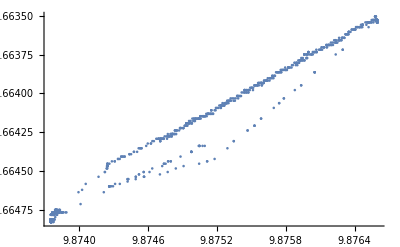

```mathematica
ListPlot[RandomSample[geoData⟦All,{1,2}⟧,1000]]
```

```mathematica
Export["/Users/tomasdecaminobeck/Documents/Wolfram Mathematica/CATIE data/Datos LIdar Drone gira2/10_sample.csv",RandomSample[geoData⟦All,{1,2}⟧,1000]]
```

/Users/tomasdecaminobeck/Documents/Wolfram Mathematica/CATIE data/Datos LIdar Drone gira2/10_sample.csv

```mathematica
Length[geoData]
```

13741